This script is a part of ANGEL project.
V 1.0.2
2018.05.11
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Variables clearing *)
```

```mathematica
importDir = "ImportData";(* Directory for importing data *)
exportDir = "ExportData";(* Directory for exporting main data *)
exportRoundDir = "RoundData";(* Subdirectory for exporting round data *)
```

```mathematica
phaseColumnName="Theta"; (* Name of column in data file with phase *)
phaseSDColumnName="ThetaSD"; (* Name of column in data file with phase *)
frequencyColumnName="Fext";(* Name of column in data file with frequency *)
timeColumnName="Time";(* Name of column in data file with time *)
intervalColumnName="Interval";(* Name of column in data file with interval *)
roundColumnName="Round";(* Name of column in data file with round *)

temperatureTimeColumnName="Time1"(* Name of column in temperature file with time *);
temperatureTemperatureColumnName="2C"(* Name of column in temperature file with temperature *);
```

```mathematica
scanningDataFileName="Continuous.dat";(* Kinetics data file *)
temperatureDataFileName="Temperature.dat";(* Temperature data files *)
```

```mathematica
scanningDataColumnNames=Import[FileNameJoin[{NotebookDirectory[],importDir,scanningDataFileName}]][[1]];(* Getting data headers *)
temperatureDataColumnNames=Import[FileNameJoin[{NotebookDirectory[],importDir,temperatureDataFileName}]][[1]];(* Getting data headers *)
If[Length[temperatureDataColumnNames]==2,temperatureTemperatureColumnName=temperatureDataColumnNames[[2]],False];(* If there are only 2 columns it is obvious which one to take *)
```

```mathematica
scanningDataRaw=Import[FileNameJoin[{NotebookDirectory[],importDir,scanningDataFileName}]][[2;;]];(* Getting experimental data *)
temperatureDataRaw=Import[FileNameJoin[{NotebookDirectory[],importDir,temperatureDataFileName}]][[2;;]];(* Getting experimental data *)
temperatureFunction=Interpolation[temperatureDataRaw,InterpolationOrder->1];(* Evaluating temperature interpolation function *)
```

```mathematica
phaseTimeData=Transpose[{(* Cutting dependency of phase from time just to show *)
scanningDataRaw[[All,Position[scanningDataColumnNames,timeColumnName][[1,1]]]],
scanningDataRaw[[All,Position[scanningDataColumnNames,phaseColumnName][[1,1]]]]
}];
phaseSDTimeData=Transpose[{(* Cutting dependency of phase standart deviation from time just to show *)
scanningDataRaw[[All,Position[scanningDataColumnNames,timeColumnName][[1,1]]]],
scanningDataRaw[[All,Position[scanningDataColumnNames,phaseSDColumnName][[1,1]]]]
}];
temperatureTimeData=Transpose[{(* Cutting dependency of temperature from time just to show *)
temperatureDataRaw[[All,Position[temperatureDataColumnNames,temperatureTimeColumnName][[1,1]]]],
temperatureDataRaw[[All,Position[temperatureDataColumnNames,temperatureTemperatureColumnName][[1,1]]]]
}];
```

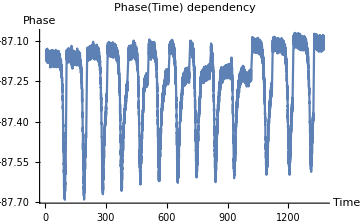
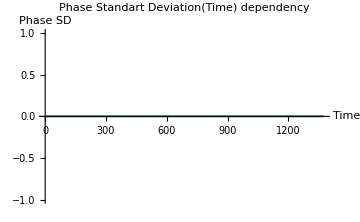
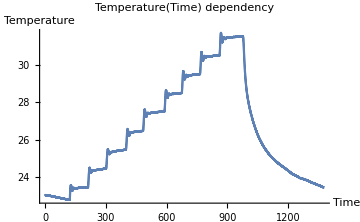

```mathematica
{ListPlot[phaseTimeData,PlotRange->All, Joined->True,ImageSize->Medium,AxesLabel->{"Time","Phase"},PlotLabel->"Phase(Time) dependency"],
ListPlot[phaseSDTimeData,PlotRange->All, Joined->True,ImageSize->Medium,AxesLabel->{"Time","Phase SD"},PlotLabel->"Phase Standart Deviation(Time) dependency"],
ListPlot[temperatureTimeData,PlotRange->All, Joined->True,ImageSize->Medium,AxesLabel->{"Time","Temperature"},PlotLabel->"Temperature(Time) dependency"]}(* Plotting data from above *)
```

```mathematica
Rounds=DeleteDuplicates[scanningDataRaw[[All,Position[scanningDataColumnNames,roundColumnName][[1,1]]]]];(* Getting all rounds *)
```

```mathematica
KineticsMin=ParallelTable[(* For every round *)
RoundData=Select[scanningDataRaw,#[[Position[scanningDataColumnNames,roundColumnName][[1,1]]]]==Rounds[[j]]&];(* Getting round data *)
MinPhase=Min[RoundData[[All,Position[scanningDataColumnNames,phaseColumnName][[1,1]]]]];(* Getting phase minimum *)
MinPhasePosition=Position[RoundData[[All,Position[scanningDataColumnNames,phaseColumnName][[1,1]]]],MinPhase][[1,1]];(* Getting position *)
ResonanceFrequency=RoundData[[All,Position[scanningDataColumnNames,frequencyColumnName][[1,1]]]][[MinPhasePosition]];(* Getting frequency *)
ResonanceTime=RoundData[[All,Position[scanningDataColumnNames,timeColumnName][[1,1]]]][[MinPhasePosition]];(* Getting time *)
ResonanceTemperature=temperatureFunction[ResonanceTime];(* Getting temperature *)
{ResonanceTemperature,ResonanceFrequency}(* Exporting calculated point *)
,{j,Length[Rounds]-1}(* Last round can be not full, let's ignore it *)
];
```

```mathematica
KineticsMin//TableForm
```

22.83401265764636921 | 2.69865625×10^6
23.44699999999999918 | 2.69852125×10^6
24.432999999999999829 | 2.69833625×10^6
25.446000000000001506 | 2.69815075×10^6
26.46176543247712799 | 2.69795125×10^6
27.48742168619343592 | 2.69778075×10^6
28.485455696396432815 | 2.697586×10^6
29.495299999809224687 | 2.697396×10^6
30.490999999999999659 | 2.697216×10^6
31.497354430573293923 | 2.69700625×10^6
25.429999999999999716 | 2.69818575×10^6
24.29412500038144249 | 2.698436×10^6
23.73570370351430952 | 2.698526×10^6

```mathematica
linear[A_,B_,x_] := A x+B;(* Linear fitting function *)
```

```mathematica
KprtFit = NonlinearModelFit[KineticsMin,linear[A,B,x],{{A,1},{B,1}},x];(* Fitting *)
parametricTableKprtFit = KprtFit["ParameterTable"];(* Getting fitting parameters table, and coefficients and their errors *)
Kprt=parametricTableKprtFit[[1,1,2,2]];(* Evaluating Kprt *)
δKprt=Abs[parametricTableKprtFit[[1,1,2,3]]];(* Evaluating Kprt error *)
F0=parametricTableKprtFit[[1,1,3,2]];(* Evaluating Frequency at 0^o C *)
```

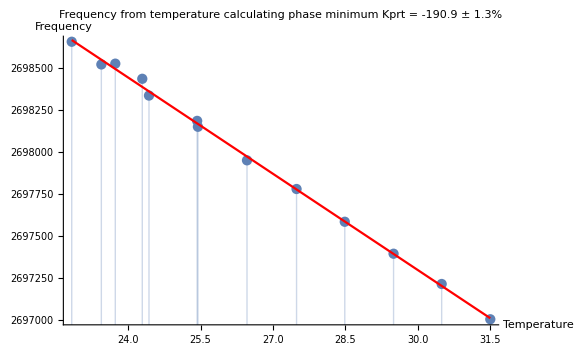

```mathematica
plt=Show[
ListPlot[KineticsMin,PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis,
AxesLabel->{"Temperature","Frequency"},PlotLabel->"Frequency from temperature calculating phase minimum"<>"\n"<>"Kprt = "<>ToString[N[Round[100×Kprt]/100]]<>" ± "<>ToString[N[Round[1000×Abs[δKprt/Kprt]]/10]]<>"%"],
Plot[F0+Kprt frequency,{frequency,Min[KineticsMin[[All,1]]],Max[KineticsMin[[All,1]]]},PlotRange->All,ImageSize->Large,ColorFunction->Function[{x,y},Red]]
](* Plotting kinetics min without fitting *)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],exportDir,"Kprt.png"}],plt];(* Exporting plot from above *)
Export[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsMin.xlsx"}],Prepend[KineticsMin,{"Temperature","Frequency"}]];(* Exporting data from plot from above *)
```